# 时间序列

## 1. 定义

时间序列的定义如下：
		1.	TimeSeriespaclet:ref/TimeSeries[{{t_1,v_1},{t_2,v_2}…}]
表示由时间数值对 {t_i,v_i} 指定的时间序列.
			
	 2.	TimeSeriespaclet:ref/TimeSeries[{v_1,v_2,…},tspec] 
表示在由 tspec 指定的时间处具有数值 v_i 的时间序列.

```mathematica
TimeSeries
```

TimeSeries

## 2. 自己创建一个时间序列

### 2.1 第二种定义

```mathematica
v = {2,1,6,5,7,4};
t = {1,2,5,10,12,15};

ts = TimeSeries[v, {t}]
```

TimeSeries[…]

### 2.2 第一种定义

直接简单的构造成：[{{t1,v1},{t2,v2},…}

```mathematica
ts22 = Table[{t[[i]], v[[i]]}, {i, 1, 6}];
ts2 = TimeSeries[ts22]
```

TimeSeries[…]

### 2.3 第三种定义：直接输入 TimeSeries

下面是一个股票价格的数据

```mathematica
ts3 = TimeSeries[…];
ts3
```

TimeSeries[…]

### 2.4 自定义时刻选择

1. 创建开始于 t==10 的时间序列：ts=TimeSeries[v, {10}];
2. 使用从 10 到 50 的均匀间隔的时间：ts=TimeSeries[v, {10,50}];
3. 创建时间从 1 到 20，步长为 2 的时间序列：ts=TimeSeries[v, {1,20,2}];
4. 给出使用的日期范围：ts=TimeSeries[v, {“2001”, ”2012”}];
5. Automatic 参数：ts = TimeSeries[v, Automatic];

```mathematica
ls = List[1, 20, 2]
```

{1,20,2}

### 2.5 可视化时间序列

1. 常规的显示：ListLinePlot[ts]
2. 路径函数显示：Plot[ts[“PathFunction”][t], {t,1,15}]

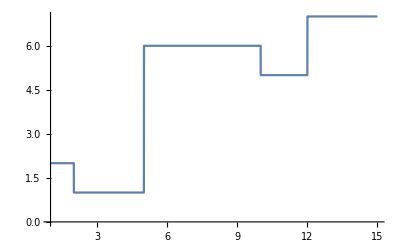

```mathematica
tsfun=TimeSeries[…];

Plot[tsfun["PathFunction"][t], {t,1,15}]
```

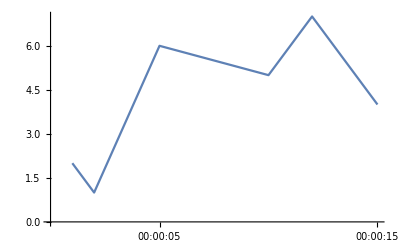

-Graphics-

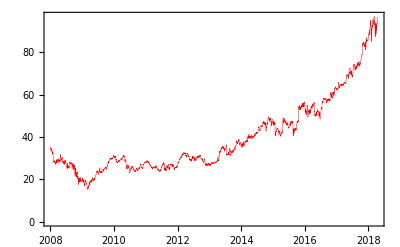

```mathematica
ListLinePlot[ts, AxesOrigin->{0, 0}]
ListLinePlot[ts2, AxesOrigin->{0, 0}]
DateListPlot[ts3, PlotStyle->{Thickness[0.0008], Red}]
```

获取某天的股票数据

```mathematica
ts3["May 24, 2009"]
```

20.045

整个日期范围内的股票平均价格

```mathematica
Mean[ts3]
```

39.6527

## 3. 时间序列的常用操作

### 3.1 提取时间序列的一部分

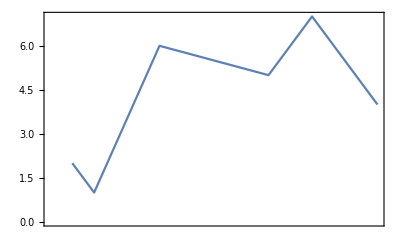
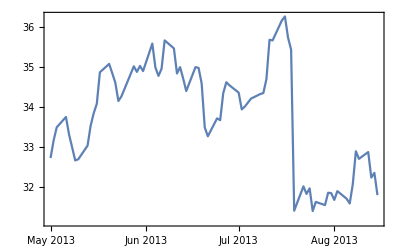

```mathematica
win=TimeSeriesWindow[ts3, {{2013,5,1}, {2013,8,15}}];
DateListPlot[#]&/@{ts, win}
```

注意：今后尽量写为下面这种标准形式，这样可以减少出错。

start = DateObject[{1750, 1, 1}];
end = DateObject[{2015, 12, 1}];
window = TimeSeriesWindow[ts, {start, end}];

### 3.2 缺失值的处理

使用 TimeSeriesInsertpaclet:ref/TimeSeriesInsert 替换缺失值

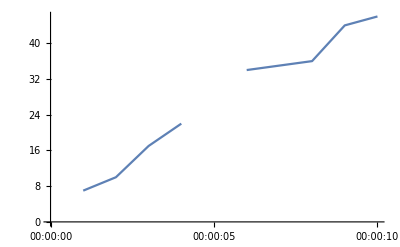

Missing[]

```mathematica
ts4=TimeSeries[{7,10,17,22,Missing[],34,35,36,44,46}, {1}];
ListLinePlot[ts4, AxesOrigin->{0, 0}]
ts4[5]
```

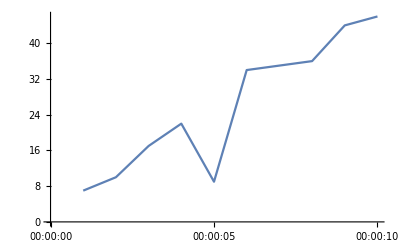

```mathematica
ins=TimeSeriesInsert[ts4, {5,9}];
ListLinePlot[ins, AxesOrigin->{0, 0}]
```

### 3.3 时间序列的移动

使用 TimeSeriesShiftpaclet:ref/TimeSeriesShift 把时间序列往前移 2

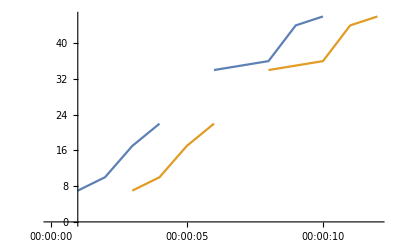

```mathematica
shts = TimeSeriesShift[ts4, 2];
ListLinePlot[{ts4, shts}]
```

### 3.4 数值特征

-Graphics- 

1. Minimum increment      -->    时间间隔
2. Data points            -->    数据点的个数
3. Output dimension       -->    时间序列值(每一个时间点对应值)的维数
4. Time                   -->    时间序列对应的时间段
5. Regular                -->    时间序列的时间间隔是否均匀
6. Resampling             -->    用于执行重采样操作的参数:根据一定的规则和方法，将时间序列对象的时间间隔调整为不同的时间间隔

1. 把时间序列中的数值求平方: ts = ts^2
2. 使用 TimeSeriesMappaclet:ref/TimeSeriesMap 求向量值时间序列每一个时刻的分量之和: mp=TimeSeriesMap[Total,ts]
3. 时间序列的 Meanpaclet:ref/Mean：Mean[ts]//N
4. 均值只取决于数值：Mean[ts[“Values”]]//N
5. 滑动平均:avg = MovingAverage[ts, 10]; 和 TimeSeriesAggregate[ts, 10];
6. 提取时间序列的值，时间节点, 时间数值对：ts[“Values”], ts[“Times”], ts[“Path”]

#### 时间序列基本信息提取

```mathematica
ts
ts["Values"]
ts["Times"]
ts["Path"]
```

TimeSeries[…]

{2,1,6,5,7,4}

{1,2,5,10,12,15}

{{1,2},{2,1},{5,6},{10,5},{12,7},{15,4}}

#### 时间序列的操作

```mathematica
(* 1.滑动平均:一次移动一位 *)

MovingAverage[ts, 2]["Values"]
(* 不重叠的窗口上的"滑动"平均：一次移动一个窗口长度 *)
(* 注意：一定的要提取出Values进行操作，不能直接在时间序列上操作 *)
TimeSeriesAggregate[ts["Values"], 2]
```

{3/2,7/2,11/2,6,11/2}

{3/2,11/2,11/2}

```mathematica
(* 2.向量值时间序列每一个时刻的分量之和 *)

ts6 = TimeSeries[{{1, 2}, {3, 4}, {5, 6}}, {1}]
(* 注：这里的{1}没有写为{1, 2, 3}可以看作是一种特殊的用法 *)
ts6["Values"]
TimeSeriesMap[Total, ts6]["Path"]
```

TimeSeries[…]

{{1,2},{3,4},{5,6}}

{{1,3},{2,7},{3,11}}

```mathematica
(* 3.平均值 *)

Mean[ts]
(* 因为是向量值的时间序列，且维数为2，所以各个分量（一共两个分量）都有平均值 *)
Mean[ts6]
```

25/6

{3,4}

#### 指定窗口

其实就是按照一定的时间间隔提取数据进行分析

```mathematica
data = FinancialData["SP500", "2000"]
```

TimeSeries[…]

```mathematica
(* 设置各种时间窗口的大小（时间间隔大小）*)

w = {{3,"Week"}, {2,"Day"}};    (* 3周2天 *)
w2 = {1, "Year"};                (* 1年 *)
w3 = {1, "Month"};               (* 1月 *)
```

```mathematica
mvar = TimeSeriesAggregate[data, w]
mvar2 = TimeSeriesAggregate[data, w2]
mvar3 = TimeSeriesAggregate[data, w3]
```

TimeSeries[…]

TimeSeries[…]

TimeSeries[…]

#### 时间窗口对齐

支持左中右对齐，默认居中对齐；（其实就是确定一个时间段的值对应的时间）

比如我每3年为一个窗口作平均采样，那么每一个数据对用的时间是3个值中的
--> 最小时间值（左对齐）
--> 中间的时间值（中央对齐）
--> 最大的时间值（右对齐）

何谓中间 ??? 
1. 窗口大小n为偶数: ((n/2+1) + (n/2+2))/2     对称轴后的第一个值 --> 平均值
2. 窗口大小n为奇数: ((n+1)/2+1 + (n+1)/2+2)/2  对称轴和后面一个值平均 --> 中间值

```mathematica
data=TimeSeries[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7]}, {1}];

(* 三种对齐的区别 *)
TimeSeriesAggregate[data,{5,Center}, f]["Path"]
TimeSeriesAggregate[data,{3,Left}, f]["Path"]
TimeSeriesAggregate[data,{3,Right}, f]["Path"]
```

{{7/2,f[{x_1,x_2,x_3,x_4,x_5}]},{17/2,f[{x_6,x_7}]}}

{{1,f[{x_1,x_2,x_3}]},{4,f[{x_4,x_5,x_6}]},{7,f[{x_7}]}}

{{4,f[{x_1,x_2,x_3}]},{7,f[{x_4,x_5,x_6}]},{10,f[{x_7}]}}

#### 一个具体的应用例子

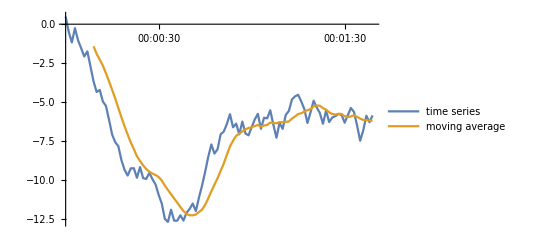

```mathematica
ts5 = TimeSeries[];
avg = MovingAverage[ts5, 10];

ListLinePlot[
	{ts5, avg}, 
	PlotLegends->Placed[
		{"time series", "moving average"}, 
		{Right, Bottom}
	]
]
```

## 4. 时间序列的参数模型拟合

### 4.1 拟合模型

使用 TimeSeriesModelFitpaclet:ref/TimeSeriesModelFit 来拟合时间序列的参数模型: tsm = TimeSeriesModelFit[ts]

```mathematica
v = {2,1,6,5,7,12};
t = {1,2,5,10,12,15};

ts = TimeSeries[v,{t}]
```

TimeSeries[…]

```mathematica
ts["Times"]
tsm = TimeSeriesModelFit[ts]
```

{1,2,5,10,12,15}

TemporalData::rsmplng: 数据没有均匀间隔，并且将自动采样到最小时间增量的解决方案 .

TimeSeriesModel[…]

弥补缺失的时间节点来使得数据分布均匀

```mathematica
intertimes = {3, 4, 6, 7, 8, 9, 11, 13, 14}; 
intertvalues = 2*#& /@ intertimes;
interts = Table[{i, 2*i}, {i, {intertimes}}][[1]]//Transpose;

Do[
	ts = TimeSeriesInsert[ts, interts[[i]]], 
	{i, 1, 9}
]

(* 结果检验 *)
ts["Times"]
ts["Values"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{2,1,6,8,6,12,14,16,18,5,22,7,26,28,12}

```mathematica
tsm = TimeSeriesModelFit[ts]
```

TimeSeriesModel[…]

### 4.2 预测

基本的预测

ARIMAProcess[1.40573,{-0.936467},1,{-0.0123835,-0.0872764},2.57298]

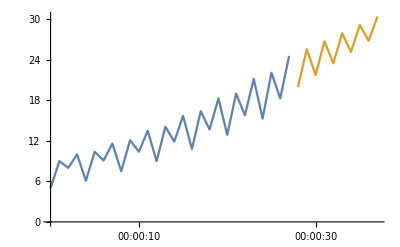

```mathematica
data = {5.,9.,8.,10.,6.1,10.4,9.1,11.6,7.5,12.1,10.4,13.5,9.,14.1,11.9,15.7,10.8,16.4,13.7,18.3,12.9,19.,15.8,21.2,15.3,22.1,18.3,24.6};
tsm = TimeSeriesModelFit[data];
Normal[tsm]
ListLinePlot[{tsm["TemporalData"], TimeSeriesForecast[tsm,{10}]}]
```

使用 TimeSeriesForecastpaclet:ref/TimeSeriesForecast 预测时间序列中未来10个数值：tsf=TimeSeriesForecast[tsm, {10}];

TemporalData[…]

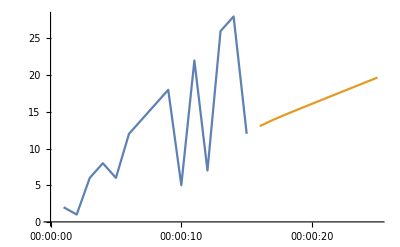

```mathematica
tsf = TimeSeriesForecast[tsm, {10}]

ListLinePlot[{ts, tsf}, AxesOrigin->{0, 0}]
```

### 4.3 为什么预测值为常数？

一方面你的数据过少，另一方面数据的趋势的确很巧合

## 5. 提取年平均值

```mathematica
ts = TimeSeries[RandomReal[{0, 1}, {100}], {{2020, 1}, Automatic, "Month"}];
```

```mathematica
meanData = TimeSeriesAggregate[ts, "Year", Mean];
```

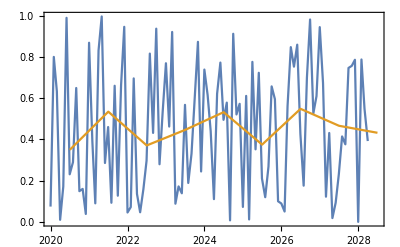

```mathematica
DateListPlot[{ts, meanData}, PlotTheme -> "Detailed"]
```

## 6. 预测股票价格

### 6.1 得到数据

TimeSeries[…]

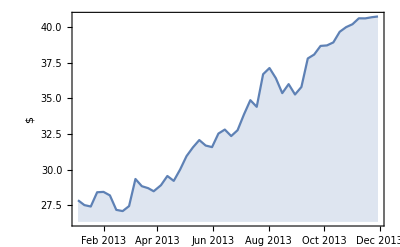

```mathematica
data=TimeSeries[
	FinancialData["SBUX","Close",
	{{2013,1,1}, {2013,12,1}, "Week"},
	Method -> "WDF"],
	TemporalRegularity->True
]

DateListPlot[data,FrameLabel->Automatic,Filling->Axis]
```

### 6.2 拟合一个 ARIMA 过程

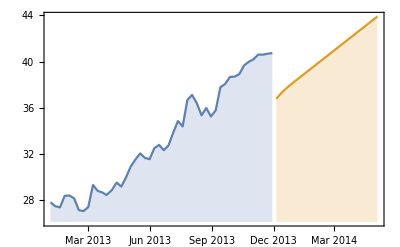

```mathematica
eproc = EstimatedProcess[
	data,
	ARIMAProcess[2,1,1],
	ProcessEstimator->"MaximumConditionalLikelihood"
];

(* 预测下半年 *)
forecast = TimeSeriesForecast[eproc, data, {26}];
DateListPlot[{data, forecast}, Filling->Axis]
```